3/4

0

400

444

BesselJ[0,x]

-BesselJ[1,x]

(2^(3/4) √π HypergeometricPFQ[{1/2},{1/8,5/8},-x^2/4])/(x^(3/4) Gamma[1/8] Gamma[5/8])

-1/(x^(3/4) Gamma[1/4])+(2^(3/4) √π HypergeometricPFQ[{1/2},{1/8,5/8},-x^2/4])/(x^(3/4) Gamma[1/8] Gamma[5/8])

ConditionalExpression[((Gamma[1/8] HypergeometricPFQ[{3/8},{1/2,7/8},-x^2/4])/Gamma[7/8]-(x Gamma[5/8] HypergeometricPFQ[{7/8},{11/8,3/2},-x^2/4])/Gamma[11/8])/(2^(3/4) Gamma[1/4]), Re[x]>0&&Im[x]==0]

ConditionalExpression[(-(Gamma[5/8] HypergeometricPFQ[{7/8},{11/8,3/2},-x^2/4])/Gamma[11/8]-(3 x Gamma[1/8] HypergeometricPFQ[{11/8},{3/2,15/8},-x^2/4])/(7 Gamma[7/8])+(7 x^2 Gamma[5/8] HypergeometricPFQ[{15/8},{19/8,5/2},-x^2/4])/(33 Gamma[11/8]))/(2^(3/4) Gamma[1/4]), Re[x]>0&&Im[x]==0]

ConditionalExpression[(-(Gamma[5/8] HypergeometricPFQ[{7/8},{1/2,11/8},-x^2/4])/(2^(3/4) Gamma[11/8])+(√π x Gamma[1/4] HypergeometricPFQ[{11/8},{3/2,15/8},-x^2/4])/(Gamma[-3/8] Gamma[15/8]))/Gamma[1/4], Re[x]>0&&Im[x]==0]

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

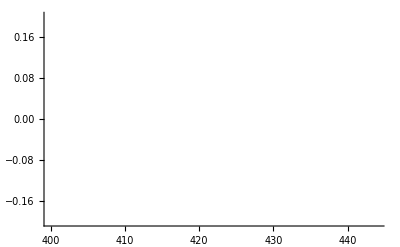

```mathematica
(*Input parameters*)
alpha=75/100                               (*alpha*)
k=0                            (*k>0 in e^(k x)*)
lb=400                          (*plot lower bound*)
ub=444                         (*plot upper bound*)
(*Riemann official *)
fun[x_] = BesselJ[k, x]
dfun[x_] = D[fun[x],x]
rieMat=FractionalD[fun[x],{x,alpha}]
(*Caputo official *)
capMat=CaputoD[fun[x],{x,alpha}]
(*Liouville *)
i1 = 1/Gamma[1-alpha]Integrate[(xi-x)^(-alpha)fun[xi],{xi,x,Infinity}]
lio = D[i1,x]
(*LiouvilleInvert *)
i2 = 1/Gamma[1-alpha]Integrate[(xi-x)^(-alpha)dfun[xi],{xi,x,Infinity}]
(*pot routines*)
pR1=Plot[rieMat,{x,lb,ub},PlotStyle->{Orange,Dashed,Thick}]
pC1=Plot[capMat,{x,lb,ub},PlotStyle->{Blue,Dotted,Thick},PlotRange->All]
pL1=Plot[lio       ,{x,lb,ub},PlotStyle->{Purple,Thick},PlotRange->All]
pL2=Plot[i2         ,{x,lb,ub},PlotStyle->{Green,Thick},PlotRange->All]
(*errors:official versus derived in ex(3.4.2)*)

(*final output*)
Show[{pR1,pC1,pL1,pL2},PlotRange->{{lb,ub},{-0.2,0.2}}]
```